```mathematica
(* ===============================Symbolic function equivalence===============================*)ClearAll[normalize,EquivalentFunctions,IntVars,RealVars,f,g];

(*Normalize control flow into mathematical form*)
normalize[expr_]:=PiecewiseExpand@FunctionExpand@expr;

(*Equivalence checker*)
EquivalentFunctions[f_,g_,vars_List,assumptions_:True]:=Module[{lhs,rhs},lhs=normalize[f@@vars];
rhs=normalize[g@@vars];
FullSimplify[lhs==rhs,assumptions]];

(*Domain helpers*)
IntVars[vars__]:=And@@(Element[#,Integers]&/@{vars});
RealVars[vars__]:=And@@(Element[#,Reals]&/@{vars});

(* ===============================Example:piecewise equivalence===============================*)

f[x_,y_]:=If[x>0,x+y,y-x]
g[x_,y_]:=y+Abs[x]

EquivalentFunctions[f,g,{x,y},RealVars[x,y]]
```

True

```mathematica
(* ============================================1D Ising model with Kawasaki dynamics Sites:{0,1}============================================*)ClearAll[initializeLattice,energy,deltaEnergy,kawasakiStep,evolve,latticePlot];

(*Initialize lattice with fixed density*)
initializeLattice[L_,density_:0.5]:=Module[{n=Round[L density]},RandomSample[Join[ConstantArray[1,n],ConstantArray[0,L-n]]]];

(*Hamiltonian*)
energy[lattice_,J_:1]:=Module[{L=Length[lattice]},-J Sum[lattice[[i]] lattice[[Mod[i,L]+1]],{i,1,L}]];

(*Energy change for Kawasaki swap*)
deltaEnergy[lattice_,i_,J_:1]:=Module[{L=Length[lattice],a,b,left,right,before,after},a=lattice[[i]];
b=lattice[[Mod[i,L]+1]];
(*Only if swap is nontrivial*)If[a==b,Return[0]];
left=lattice[[Mod[i-2,L]+1]];
right=lattice[[Mod[i+1,L]+1]];
before=-J (left a+a b+b right);
after=-J (left b+b a+a right);
after-before];

(*One Kawasaki update*)
kawasakiStep[lattice_,β_:1,J_:1]:=Module[{L=Length[lattice],i,ΔE,new=lattice},i=RandomInteger[{1,L}];
ΔE=deltaEnergy[lattice,i,J];
If[ΔE<=0||RandomReal[]<Exp[-β ΔE],new[[{i,Mod[i,L]+1}]]=Reverse[new[[{i,Mod[i,L]+1}]]]];
new];

(*Time evolution*)
evolve[lattice_,steps_,β_:1,J_:1]:=NestList[kawasakiStep[#,β,J]&,lattice,steps];

(*Visualization*)
latticePlot[lattice_]:=ArrayPlot[{lattice},ColorRules->{0->White,1->Black},Frame->True,AspectRatio->1/10];

(* ============================================Example run============================================*)

L=50;
β=0.1;
steps=1000;

lat0=initializeLattice[L,0.5];
trajectory=evolve[lat0,steps,β];
```

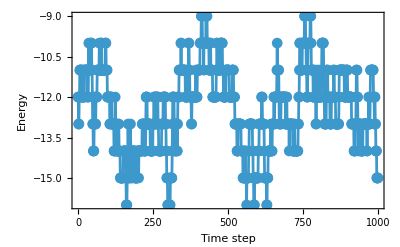

```mathematica
(* ============================================Energy vs time for 1D Ising (0/1 variables)============================================*)ClearAll[EnergyTimeSeries];

EnergyTimeSeries[trajectory_,J_:1]:=Module[{energies},energies=energy[#,J]&/@trajectory;
Transpose[{Range[0,Length[energies]-1],energies}]];

(* ============================================Example usage============================================*)

energyData=EnergyTimeSeries[trajectory,1];
ListLinePlot[energyData,Frame->True,FrameLabel->{"Time step","Energy"},PlotMarkers->Automatic,PlotRange->All]
```

```mathematica
H[x_] := x
x = {1,2,3}
x==H[x]
```

{1,2,3}

True

```mathematica
N[1/2]
```

0.5

```mathematica
1/2 //N
```

0.5

```mathematica
(* =========================================Function:TestKolmogorov Checks if a transition matrix T satisfies Kolmogorov's cycle criterion.
=========================================*)ClearAll[TestKolmogorov];

TestKolmogorov[T_?MatrixQ]:=Module[{n,states,cycles,forward,backward,allEqual},n=Length[T];
states=Range[n];
(*Generate all simple cycles of length>=3*)cycles=Flatten[Table[Permutations[states,{k}],{k,3,n}],1];
(*Function to compute product of transitions along a path*)forward[path_]:=Times@@(T[[#1,#2]]&@@@Partition[path,2,1]);
backward[path_]:=Times@@(T[[#2,#1]]&@@@Partition[path,2,1]);
(*Check Kolmogorov criterion for all cycles*)allEqual=And@@Table[forward[cycle]==backward[cycle],{cycle,cycles}];
allEqual];
```

```mathematica
T2={{0,1,0},{0,0,1},{1,0,0}};
TestKolmogorov[T2]
```

False

```mathematica
(* =========================================Symbolic Kolmogorov checker T can have symbolic elements=========================================*)ClearAll[TestKolmogorovSymbolic];

ClearAll[TestKolmogorovSymbolicAssume];

TestKolmogorovSymbolicAssume[T_?MatrixQ,assumptions_:True]:=Module[{n,states,cycles,forward,backward,allEqual},n=Length[T];
states=Range[n];
cycles=Flatten[Table[Permutations[states,{k}],{k,3,n}],1];
forward[path_]:=Times@@(T[[#1,#2]]&@@@Partition[path,2,1]);
backward[path_]:=Times@@(T[[#2,#1]]&@@@Partition[path,2,1]);
allEqual=And@@Table[Simplify[forward[cycle]==backward[cycle],assumptions],{cycle,cycles}];
allEqual];

T={{1-x,x},{0,0}};

Simplify[TestKolmogorovSymbolicAssume[T,0<=x<=1&&0<=y<=1]]


T={{1-f[x]-g[y],f[x],g[y]},{h[z],1-h[z]-k[w],k[w]},{m[u],n[v],1-m[u]-n[v]}};
Simplify[TestKolmogorovSymbolicAssume[T,f[x]>=0&&g[y]>=0&&h[z]>=0&&k[w]>=0&&m[u]>=0&&n[v]>=0&&f[x]+g[y]<=1&&h[z]+k[w]<=1&&m[u]+n[v]<=1]]
```

True

g[y] h[z]==f[y] m[u]&&f[y] k[w]==h[z] n[v]&&k[w] m[u]==g[y] n[v]

```mathematica
(*3x3 symbolic transition matrix that violates detailed balance*)T={{1-f1[x]-f2[y],f1[x],f2[y]},(*row 1*){0,1-f3[z]-f4[w],f3[z]},(*row 2*){f4[w],0,1-f4[w]}               (*row 3*)};
Simplify[TestKolmogorovSymbolicAssume[T,f1[x]>=0&&f2[y]>=0&&f3[z]>=0&&f4[w]>=0&&f1[x]+f2[y]<=1&&f3[z]+f4[w]<=1&&f4[w]<=1]]
```

```mathematica
f3[z] f4[w]==0&&y f3[z]==0&&y f4[w]==0

(*So need to check null space and make sure all pi > 0 so that there exists a stationary distribution*)
```